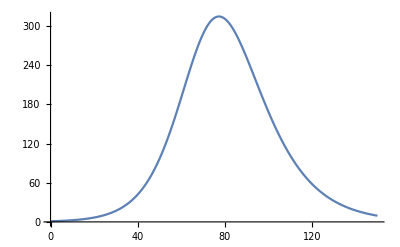

```mathematica
Clear["Global`*"];

EulerMethod[s0_, beta_,alpha_, range_]:=(
rangeStart = range[[1]];
rangeEnd = range[[2]];
steps = Table[x, {x, rangeStart, rangeEnd}];

idata[0]=1;
sdata[0]=s0;

(*Print["sdata[0] = ",sdata[0]];
Print["idata[0] = ",idata[0]];*)

For[i = 0, i <Length[steps]-1,i++,
	x=steps[[i+1]];
	nextX = steps[[i + 2]];
	sdata[nextX]=sdata[x]-beta sdata[x] idata[x];
	idata[nextX]=idata[x]+beta sdata[x] idata[x]-alpha idata[x];
	(*Print["sdata[",nextX,"] = ",sdata[nextX]];
	Print["idata[",nextX,"] = ",idata[nextX]];*)
	sdata[nextX]=Max[0, Min[n, sdata[nextX]]];
	idata[nextX]=Max[0, Min[n, idata[nextX]]]];

Table[{i, idata[i]}, {i, rangeStart, rangeEnd}]
);

range={0, 150};
beta = 0.0001;
alpha = 0.1;
n=1999;

points=EulerMethod[n, beta,alpha,range];
ListPlot[points,PlotRange->All, Joined->True]
```